```mathematica
(*Mean value theorem solver*)
```

```mathematica
mvtSolver[function_]:=Solve[Evaluate@function==Integrate[Evaluate@function,{x,a,b}/.{a->bound1,b->bound2}]/(b-a)/.{a->bound1,b->bound2}&&x∈Interval[{0,1}],x]//N
```

```mathematica
mvtSolver[f1[x]]
```

{{x→-0.57735},{x→0.57735}}

```mathematica
f1[x]:=x^2
mvtSolver[function_]:=Solve[Evaluate@function==Integrate[Evaluate@function,{x,a,b}/.{a->bound1,b->bound2}]/(b-a)/.{a->bound1,b->bound2},x]//N
bound1=0;bound2=1;
Solve[Evaluate@f1[x]==Integrate[Evaluate@f1[x],{x,a,b}/.{a->bound1,b->bound2}]/(b-a)/.{a->bound1,b->bound2},x]//N
```

mvtSolver[function_,bounds]

0

1

{{x→-0.57735},{x→0.57735}}

ⅇ^(5/2)/(7/2+1/2 (-5/2+x)^2-1/6 (-5/2+x)^3+1/24 (-5/2+x)^4-1/120 (-5/2+x)^5-x)

{{x→ConditionalExpression[0.541325+(0.+6.28319 ⅈ) C[1],C[1]∈Integers]}}

{{x→0.542196},{x→2.18979-4.26039 ⅈ},{x→2.18979+4.26039 ⅈ},{x→6.28912-2.39148 ⅈ},{x→6.28912+2.39148 ⅈ}}

1.71828

1.71978

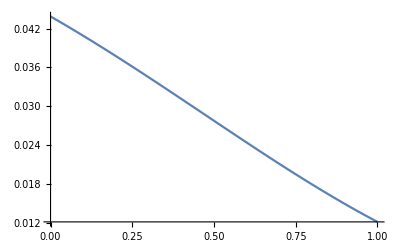

```mathematica
(*Test for Exponential and Pade Exp*)
Clear[x]
f[x]:=PadeApproximant[Exp[x],{x,((5b-a)/2),{a,5b}}]/.{a->0,b->1}
f[x]
f1[x]:=Exp[x]
Solve[Evaluate@f1[x]==Integrate[Evaluate@f1[x],{x,a,b}/.{a->0,b->1}]/(b-a)/.{a->0,b->1},x]//N
Solve[Evaluate@f[x]==Re@Integrate[Evaluate@f[x],{x,a,b}/.{a->0,b->1}]/(b-a)/.{a->0,b->1},x]//N
Integrate[Exp[x],{x,0,1}]//N
Exp[x]/.x->0.5421959605628446//N
Plot[{Evaluate[Evaluate[f[x]/.{a->0,b->1}]-Evaluate[f1[x]]]},{x,0,1}]
```

```mathematica
b1
```

b1

```mathematica
b1=0
b2=1
test[x]:=x^2
pade[x]:=PadeApproximant[Evaluate@test[x],{x,((5b-a)/2),{a,5b}}]/.{a->0,b->1}
Solve[test[x]==Evaluate[Integrate[test[x],{x,a,b}]/(b-a)/.{a->0,b->1}],x]//Timing//TableForm
Solve[Evaluate[pade[x]]==Evaluate[Integrate[pade[x],{x,a,b}]/(b-a)/.{a->0,b->1}],x]//Timing//TableForm
```

0

1

0.01139 | 
x→-1/(√3) | x→1/(√3)

$Aborted

```mathematica
Evaluate[pade[x]]
```

pade[x]

```mathematica
Evaluate@Integrate[Evaluate@test[x],{x,a,b}]/(b-a)/.{a->0,b->1}
```

1/3

```mathematica
Evaluate[(Integrate[Evaluate@test[x],{x,a,b}]/(b-a))/.{a->0,b->1}]
```

1/3

```mathematica
Solve[test[x]==Evaluate[Integrate[test[x],{x,a,b}]/(b-a)/.{a->0,b->1}],x]//Timing//TableForm
```

0.011994 | 
x→-1/(√3) | x→1/(√3)

```mathematica
Solve[f1[x]==Evaluate@Integrate[Evaluate@test[x],{x,a,b}]/(b-a),x]/.{a->0,b->1}//N//Timing
```

{0.015314,{{x→ConditionalExpression[2.80176+6.28319 C[1],C[1]∈Integers]},{x→ConditionalExpression[0.339837+6.28319 C[1],C[1]∈Integers]}}}

```mathematica
Solve[f[x]==Re@Integrate[Evaluate@pade[x],{x,a,b}]/(b-a),x]/.{a->0,b->1}//N//Timing
```

0

1

$Aborted

{0.026624,{{x→ConditionalExpression[0.339837+6.28319 C[1],C[1]∈Integers]},{x→ConditionalExpression[2.80176+6.28319 C[1],C[1]∈Integers]}}}